```mathematica
ClearAll["Global`*"]

V[x_,y_]=L/2(1/(√ρ)(x-xs)-√ρ(y-xs))^2+f[y]-f[xs];
yk1=xk-1/L g[xk];
xk1=yk1+β (yk1-yk);
ineq1=f[yk1]-f[xk]+g[yk1](xk-yk1)+1/(2L)(g[yk1]-g[xk])^2+μ/(2(1-μ/L))(yk1-xk-1/L(g[yk1]-g[xk]))^2;
λ1=1;
ineq2=f[xk]-f[xs]+g[xk](xs-xk)+1/(2L)(g[xk])^2+ μ/(2(1-μ/L))(xk-xs-1/L g[xk])^2;
λ2=1-ρ;
ineq3=f[xk]-f[yk]+g[xk](yk-xk);
λ3=ρ;
expr1=λ1 ineq1 + λ2 ineq2 + λ3 ineq3//FullSimplify;
expr2=V[xk1,yk1]- ρ V[xk,yk]+1/(2(L-μ))g[yk1]^2+(1-ρ)/(2 L) g[xk]^2+ (L(ρ^3-β^2))/(2 ρ)(yk-xs+ (β ρ - β (β+1)+ρ^2)/(β^2-ρ^3)(xk-xs)+(β^2-β ρ + β - ρ^2)/(β^2 L - L  ρ^3) g[xk])^2+L^2(1-ρ) (μ/L ρ (2 β ρ - β (β+2)+ρ)+(ρ-1)(β-ρ)^2)/(2 (ρ^3-β^2)(L-μ))(xk-xs-1/L g[xk])^2;
expr1-expr2//FullSimplify
```

0

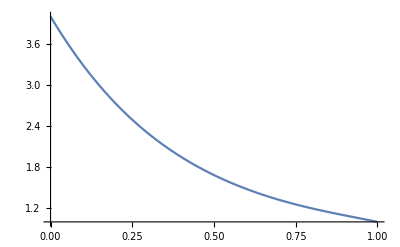

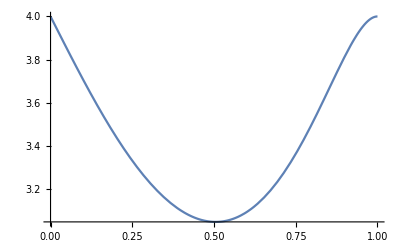

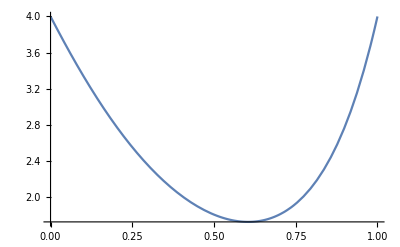

```mathematica
p1 = -x^8+4x^7-8x^6+9x^5-4x^4-4x^3+9x^2-8x+4;
p2 = -x^11 + 2x^9 -3x^8-x^7+6x^6-3x^5-3x^4+6x^3-3x+4;
p4 = x^8-x^7+2x^6+3x^5-7x^4+5x^3+4x^2-7x+4;
Plot[p1,{x,0,1}]
Plot[p2,{x,0,1}]
Plot[p4,{x,0,1}]
```